```mathematica
square = Rectangle[{-1,-1},{1,1}];
(* square = Rectangle[]; *)
boundary=RegionBoundary[square]⟦1⟧;
nodes=Most@boundary;
n=Length@nodes;
ListPlot[
nodes,
LabelingFunction->(Position[nodes,#]&),
AspectRatio->1,PlotStyle->{PointSize->Large},ImageSize->Small
];
```

```mathematica
standardBasisFunctions={
1&,
#⟦1⟧&,
#⟦2⟧&,
#⟦1⟧#⟦2⟧&
};
H=Table[standardBasisFunctions⟦j⟧[nodes⟦i⟧],{i,1,n},{j,1,n}];
Subscript[H, inv]=Inverse@H;
Subscript[H^T, inv]=Transpose@Subscript[H, inv];
```

```mathematica
Ψ=Table[
With[{i=i},Sum[Subscript[H^T, inv]⟦i,j⟧standardBasisFunctions⟦j⟧@#,{j,1,n}]&],{i,1,n}];
Simplify[Through[Ψ[{ξ,η}]]]// MatrixForm;
```

```mathematica
(* NIntegrate is bad in our case since it does a lot of unnecessary work *) (* We know that we are using polynomials => quick exact gaussian quadrature formulas *)
locWeights=N@{{{-1/(√3),-1/(√3)},1},{{1/(√3),-1/(√3)},1},{{-1/(√3),1/(√3)},1},{{1/(√3),1/(√3)},1}};
numericIntegrate[fSymb_]:=Sum[locWeights⟦i,2⟧(fSymb/.{ξ->locWeights⟦i,1,1⟧,η->locWeights⟦i,1,2⟧}),{i,1,Length@locWeights}]
```

```mathematica
(* The list of shape functions and its gradient when evaluated at ξ and η *)
ψ=Simplify@{Through[Ψ[{ξ,η}]]};
ψT=Transpose@ψ;
ψTψ=Simplify[ψT.ψ];
gradψ=Transpose@Grad[Through[Ψ[{ξ,η}]],{ξ,η}];
gradψT=Transpose@gradψ;

J[elementNodes_?MatrixQ]:=gradψ.elementNodes
(* By taking B=|J| J^-1 we end up calculating |J|/inverse once less in the integral and can directly provide formula for the values *)
B[elementNodes_?MatrixQ]:=Module[{j=J@elementNodes},
{{j⟦2,2⟧,-j⟦1,2⟧},
{-j⟦2,1⟧,j⟦1,1⟧}}
]
(* Alternatively - we may just calculate B for a given Jacobian, since we will have to calculate it in the stiffness anyway *)
BfromJ[j_?MatrixQ]:={{j⟦2,2⟧,-j⟦1,2⟧},{-j⟦2,1⟧,j⟦1,1⟧}}
```

```mathematica
localMass[elementNodes_?MatrixQ]:=numericIntegrate[Abs@Det@J[elementNodes] ψT.ψ]
localStiffness[elementNodes_?MatrixQ]:=Module[{j=J@elementNodes,b,bT,f},
b=BfromJ@j;
bT=Transpose@b;
numericIntegrate[1/(Abs@Det@j)gradψT.bT.b.gradψ ]
]
```

```mathematica
FEMMatrix[nodes_?ListQ,elements_?ListQ,localFunction_,nullNodes_:{}?ListQ]:=Module[{
globalMatrix = SparseArray@ConstantArray[0,{Length@nodes,Length@nodes}], element, quality},
For[k=1,k≤Length@elements,k++,
element = elements⟦k⟧;
quality=localFunction@nodes⟦element⟧;
For[i=1,i≤Length@element,i++,
For[j=1,j≤Length@element,j++,
globalMatrix⟦element⟦i⟧,element⟦j⟧⟧+=quality⟦i, j⟧;
];
];
];

(* We should now take into account that some of the coefficients will have to be 0 to ensure the boundary condition of u=0 *)
For[i=1,i≤Length@nullNodes,i++,
For[j=1,j≤Length@nodes,j++,
globalMatrix⟦j,nullNodes⟦i⟧⟧=0;
globalMatrix⟦nullNodes⟦i⟧,j⟧=0;
];
globalMatrix⟦nullNodes⟦i⟧,nullNodes⟦i⟧⟧=1;
];

globalMatrix
]

(* The function that assebles the global stiffness matrix *)
stiffnessMatrix[nodes_?ListQ,elements_?ListQ,nullNodes_?ListQ]:=FEMMatrix[nodes,elements,localStiffness,nullNodes]

(* The function that assebles the global mass matrix *)
massMatrix[nodes_?ListQ,elements_?ListQ,nullNodes_?ListQ]:=FEMMatrix[nodes,elements,localMass,nullNodes]
```

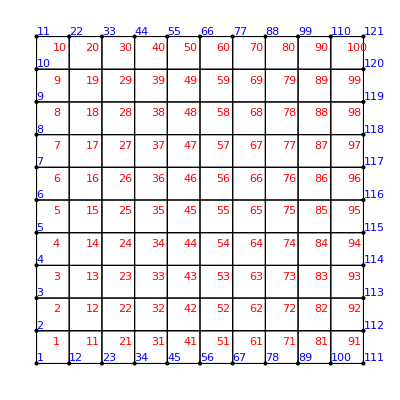

```mathematica
(* Discretization of the region *)
Ω=Rectangle[];
Needs["NDSolve`FEM`"]
mesh=ToElementMesh[Ω, "MeshOrder"-> 1,MaxCellMeasure->0.01];
mesh["Wireframe"];
Show[mesh["Wireframe"["MeshElementIDStyle"->Red]],mesh["Wireframe"["MeshElement"->"PointElements","MeshElementIDStyle"->Blue]]]
nodes = mesh["Coordinates"];
elements = mesh["MeshElements"]⟦1,1⟧;
boundary =Flatten[mesh["BoundaryElements"]⟦1,1⟧];
boundary=DeleteDuplicates[boundary];
```

```mathematica
Subscript[M, 0]=massMatrix[nodes,elements,{}];
Subscript[M, 1]=stiffnessMatrix[nodes,elements,{}];
```

```mathematica
initialU[{x_,y_}]:=If[x^2+y^2≤1/16,100,0]
α[u_]:=u
G[u_]:=u^2/2
```

```mathematica
JacN[f_,x_]:=Module[{J,m=Length[x],n=Length[f[x]],i,j,h=10^-10},J=Table[(f[x+h*UnitVector[m,i]]-f[x])/h//N,{i,1,m}];
Return[Transpose[J]];];

NewtonSolver[F_,x0_,tol_]:=Module[{xOld=x0,xNew=x0,J},While[Norm[F[xNew],2]≥tol,J=JacN[F,xOld]//N;
xNew=xOld-Inverse[J].F[xOld]//N;
xOld=xNew;];
Return[xNew]];
DoWhile[expr_,test_]:=(expr;While[test,expr])

nonStandardFEM[nodes_?ListQ,elements_?ListQ,nullNodes_?ListQ,T_,τ_,uInit_,α_,G_,M0_,M1_]:=Module[{
n=Length@nodes,m=Ceiling@(T/τ),GVec,sol,solApprox,jacobian,jacobianInv,F,h,step},
sol=ConstantArray[0,{m,n}];
sol⟦1⟧=uInit/@nodes;
(*MM=SparseArray@DiagonalMatrix[Table[Total@M0⟦i⟧,{i,1,n}]];*)
For[j=1,j<m,j++,
Print@j;
GVec=G/@sol⟦j⟧;
sol⟦j+1⟧=LinearSolve[M0,M0.sol⟦j⟧-τ M1.GVec];

step=0;
F=M0.(#-sol⟦j⟧)+τ/2 M1.(G/@#+GVec)&;
h=ConstantArray[1,n];

While[h.h≥τ&&step≤10,
jacobian=M0+τ/2 M1.DiagonalMatrix[α/@sol⟦j+1⟧];
h=LinearSolve[J,F@sol⟦j+1⟧];
sol⟦j+1⟧-=h;
step++;
];
(*solApprox=LinearSolve[M0,M0.sol⟦j⟧-τ M1.GVec];*)
(*While[Norm[solApprox-sol⟦j+1⟧]≥τ&&step≤20,
solApprox=sol⟦j+1⟧;
jacobian=M0+τ/2 M1.DiagonalMatrix[α/@sol⟦j+1⟧];
h=LeastSquares[J,F[solApprox]];
{sol⟦j+1⟧,solApprox}={solApprox-h,solApprox};
step++;
];*)
(*DoWhile[
Print@step;
step++;
sol⟦j+1⟧=solApprox;
F=M0.(sol⟦j+1⟧-sol⟦j⟧)+τ/2 M1.(G/@sol⟦j+1⟧+GVec);
jacobian=M0+τ/2 M1.DiagonalMatrix[α/@sol⟦j+1⟧];
h=LinearSolve[jacobian,F];
solApprox=sol⟦j+1⟧-h;,
Norm[solApprox-sol⟦j+1⟧]≥τ&&step≤20

];
sol⟦j+1⟧=solApprox;*)
(*For[k=1,k≤8,k++,
F=M0.(sol⟦j+1⟧-sol⟦j⟧)+τ/2 M1.(G/@sol⟦j+1⟧+GVec);
jacobian=M0+τ/2 M1.DiagonalMatrix[α/@sol⟦j+1⟧];
(*jacobian=JacN[MM.(#-sol⟦j⟧)+τ/2 M1.(G/@#+GVec)&,sol⟦j+1⟧];*)
h=LinearSolve[jacobian,F];
sol⟦j+1⟧-=h;
];*)
];

sol
]
```

```mathematica
(* Solve the equation *)
T=0.005;
τ=10^-4;
q=nonStandardFEM[nodes,elements,{},T,τ,initialU,α,G,Subscript[M, 0],Subscript[M, 1]];
u=Table[Interpolation[Thread[{nodes,q⟦k⟧}],InterpolationOrder->1],{k,1,Length@q}];
```

1

2

3

$Aborted

3

2

1

49

48

47

46

45

44

43

42

41

40

39

38

37

36

35

34

33

32

31

30

29

28

27

26

25

24

23

22

21

20

19

18

17

16

15

14

13

12

11

10

9

8

7

6

5

4

3

2

1

0

$Aborted

```mathematica
(* Contour plot of the solution *)
Manipulate[
ContourPlot[
{u⟦k⟧[x,y]},
{x,y}∈Ω,
PlotLabel->"Contour plot of u",PlotRange->All],
{k,1,Length@u,1}
]
```

ContourPlot::idomdim: {x,y}∈Ω does not have a valid dimension as a plotting domain.

Part::partd: Part specification u⟦1000⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 1000 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 1000 of {«1»,InterpolatingFunction[{{0.,1.},{0.,1.}},«3»,{Automatic,«9»}],«47»,InterpolatingFunction[{{0.,1.},{0.,1.}},{5,3,0,{11,11},{2,2},0,0,0,0,Automatic,{},{},False},{{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.},{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}},{«1»},{Automatic,Automatic}]} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
jacobian
```

{{-3.44917090304491×10^9630,119,0.},119,{0.,119,-62}}
 |  |  |  |

```mathematica
MatrixPlot@Subscript[M, 0];
MatrixPlot@Subscript[M, 1];
```

```mathematica
Subscript[M, 0] // MatrixForm;
Subscript[M, 1] // MatrixForm;
Inverse[DiagonalMatrix[Table[Total@Subscript[M, 0] ⟦i⟧,{i,1,Length@Subscript[M, 0]}]] ] // MatrixForm;
```

```mathematica
q // MatrixForm;
```

```mathematica
Subscript[M, 0]⟦1,1⟧
Subscript[M, 1]⟦1,1⟧
```

0.000307787

0.666667

```mathematica
Inverse@Subscript[M, 1]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.666667,-0.166667,0.,0.,0.,0.,0.,0.,0.,0.,«390»},{-0.166667,1.33333,-0.166667,0.,0.,0.,0.,0.,0.,0.,«390»},«7»,{0.,0.,0.,0.,0.,0.,0.,0.,-0.166667,1.33333,«390»},«390»} may contain significant numerical errors.

{1}
 |  |  |  |

```mathematica
sol[[2]]
sol[[1000]]
```

{92.2554,89.1106,69.1078,30.2075,1.5745,0.00481884,4.19211×10^-8,3.26194×10^-18,1.94174×10^-38,4.58516×10^-58,4.03487×10^-70,89.1106,82.2073,62.3451,22.2871,1.28525,0.00367996,3.28401×10^-8,2.51601×10^-18,1.5071×10^-38,3.94836×10^-58,3.52589×10^-70,69.1078,62.3451,31.5443,11.9808,0.533973,0.00162629,1.35411×10^-8,1.05577×10^-18,6.22468×10^-39,2.4085×10^-58,2.36755×10^-70,30.2075,22.2871,11.9808,1.06142,0.120708,0.000249751,2.25613×10^-9,1.57044×10^-19,9.49439×10^-40,1.02179×10^-58,1.15881×10^-70,1.5745,1.28525,0.533973,0.120708,0.000963128,0.0000121428,5.21024×10^-11,4.24402×10^-21,2.05675×10^-41,2.48997×10^-59,3.92882×10^-71,0.00481884,0.00367996,0.00162629,0.000249751,0.0000121428,7.73258×10^-10,1.22873×10^-13,2.26223×10^-24,1.50105×10^-44,2.54726×10^-60,6.89909×10^-72,4.19211×10^-8,3.28401×10^-8,1.35411×10^-8,2.25613×10^-9,5.21024×10^-11,1.22873×10^-13,4.98274×10^-22,1.25815×10^-29,5.23811×10^-51,1.29779×10^-61,-2.47109×10^-74,3.26194×10^-18,2.51601×10^-18,1.05577×10^-18,1.57044×10^-19,4.24402×10^-21,2.26223×10^-24,1.25815×10^-29,2.06864×10^-46,1.04383×10^-54,1.92059×10^-64,-2.93765×10^-73,1.94174×10^-38,1.5071×10^-38,6.22468×10^-39,9.49439×10^-40,2.05675×10^-41,1.50108×10^-44,5.01965×10^-51,2.48465×10^-54,3.56452×10^-63,1.99915×10^-67,-3.98872×10^-74,5.73734×10^-58,4.89317×10^-58,3.11075×10^-58,1.34792×10^-58,3.87771×10^-59,4.4552×10^-60,1.53392×10^-61,1.17377×10^-64,5.76588×10^-67,1.82036×10^-73,-1.96741×10^-75,3.58096×10^-69,3.20792×10^-69,2.29457×10^-69,1.29052×10^-69,5.53226×10^-70,1.70779×10^-70,3.39083×10^-71,3.24524×10^-72,6.3338×10^-74,-1.82128×10^-75,9.63931×10^-77}

{5.33364,5.3317,5.32604,5.3172,5.30603,5.29358,5.28108,5.26975,5.26073,5.25492,5.25291,5.3317,5.32974,5.32407,5.3152,5.30398,5.29149,5.27894,5.26756,5.2585,5.25267,5.25066,5.32604,5.32407,5.31833,5.30936,5.29802,5.28539,5.2727,5.2612,5.25204,5.24614,5.2441,5.3172,5.3152,5.30936,5.30024,5.28871,5.27586,5.26295,5.25125,5.24193,5.23592,5.23385,5.30603,5.30398,5.29802,5.28871,5.27693,5.26381,5.25062,5.23866,5.22913,5.223,5.22088,5.29358,5.29149,5.28539,5.27586,5.26381,5.25038,5.23687,5.22463,5.21487,5.20859,5.20642,5.28108,5.27894,5.2727,5.26295,5.25062,5.23687,5.22305,5.21052,5.20053,5.19409,5.19187,5.26975,5.26756,5.2612,5.25125,5.23866,5.22463,5.21052,5.19772,5.18751,5.18094,5.17867,5.26073,5.2585,5.25204,5.24193,5.22913,5.21487,5.20053,5.18751,5.17714,5.17045,5.16814,5.25492,5.25267,5.24614,5.23592,5.223,5.20859,5.19409,5.18094,5.17045,5.16369,5.16136,5.25291,5.25066,5.2441,5.23385,5.22088,5.20642,5.19187,5.17867,5.16814,5.16136,5.15902}

```mathematica
j
```

933